```mathematica
gEph=0.035;αG=2.53;ainm=2.46 10^-10;ainBohr=ainm/(5.29177 10^-11);
Nagib=Sqrt[3] ainBohr^2 αG^2 gEph^2 /16;
Eph=0.7692307692307692;
LD=32.30769230769231;
LG=37.1213101534543;Dcut=LG;

ImS[ω_]=1/100000000000000000000+If[Abs[-1+ω]<0.7692307692307692,0,Nagib Abs[ω-Sign[ω-1] Eph]];

ReS[ω_]=0.0029194846882482015 (9.627235691523993+(-0.7692307692307692+ω) Log[(1.7692307692307692-ω)^2]+(0.7692307692307692-ω) Log[(32.30769230769231-ω)^2]-0.7692307692307692 Log[(-0.23076923076923084+ω)^2]-ω Log[(-0.23076923076923084+ω)^2]+1.5384615384615383 Log[(0.7692307692307692+ω)^2]+2 ω Log[(0.7692307692307692+ω)^2]-0.7692307692307692 Log[(37.1213101534543+ω)^2]-ω Log[(37.1213101534543+ω)^2])-Log[Abs[-32.30769230769231+ω]]/(100000000000000000000 π)+Log[Abs[8.5+ω]]/(100000000000000000000 π);
```

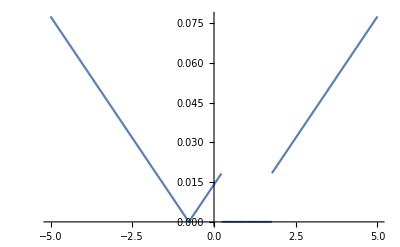

```mathematica
Plot[ReS[w],{w,-5,5}]
```